# Pieces of Art Appreciated with Wolfram Language Machine Learning

Applying machine learning and the Wolfram Language functionality to learn about five of the most famous painting artist in history.

Diego Gutierrez Coronel, Jun. 24,  2018

Mathematica and the Wolfram Language is known for being a symbolic language that also works well for plotting and visualisation. However it can be used for much more, with a simple but broad functionality for Machine Learning. It can be very useful to analyze data, simulate processes, either scientific or mathematical, and even develop software for different applications. Art appreciation and categorization can be though of as a subjective topic not related with computation. However, nowadays the tools developed by machine learning have already been used to study art history, style, among others.

## From Renaissance to Post-Impressionism

We will apply some of the Machine Learning tools in the Wolfram Language to look at five different artist as shown in the list created below. Each one of the artist belonging to different periods of time and stylistic movements in art. Representing the Italian Renaissance is Sandro Botticelli, form the Baroque period is Spanish artist Diego Velázquez, and his famous compatriot Pablo Picasso, figure of the Cubistic style. Additionally we have Claude Monet and Vincent van Gogh from opposing movements, Impressionism and Post-Impressionism, respectively. With the Wolfram Language, this set of strings can be converted into real-world entities that can be used symbolically.

```mathematica
paintersList = {"Sandro Boticelli", "Diego Velazquez", "Claude Monet", "Vincent Van Gogh", "Picasso"};
Interpreter["Person"][#] & /@ paintersList
```

{Sandro Botticelli,Diego Velázquez,Claude Monet,Vincent van Gogh,Pablo Picasso}

These entities contain different properties and thus we can access information and various types of data from this symbolic expressions. Here we take a random sample of five famous paintings from Picasso. We can also check the number of “Notable Artworks” Images stored under Boticelli’s Entity.

```mathematica
EntityValue[RandomSample[LinguisticAssistant["NotableArtworks"], 3], "Image"]
Length[Cases[EntityValue[EntityList[LinguisticAssistant["NotableArtworks"]],"Image"],_Image]]
```

{-Graphics-,-Graphics-,-Graphics-}

52

With the following code we assign a list of 5 lists of notable paintings from each of the artist presented.

```mathematica
paintingImages=Cases[EntityValue[
RandomSample[Interpreter["Person"][#]["NotableArtworks"], 40]
,"Image"]
,_Image]&/@paintersList;
```

We can also see the total number of paintings stored below and a sample of these.

```mathematica
Length[Flatten[paintingImages]]
paintingImages⟦4,9⟧
```

176

-Graphics-

## Color Appreciation

These paintings could be analyzed in different ways. We could for example see the distinctive colors used by each artist by taking the pixel color of all images for each of the artist and plotting it in a Chromaticity Plot.

```mathematica
colors={Blue,Red,Green,Gray,Orange};
Legended[
	Show[
		ChromaticityPlot[#1,PlotStyle->#2,Appearance-> "VisibleSpectrum"]&@@@Transpose[{paintingImages,colors}]
		(*Table[ChromaticityPlot[paintingImages[[i]],PlotStyle->colors[[i]],Appearance-> "VisibleSpectrum"],{i,1,5}]*)
	],
	SwatchLegend[colors,paintersList]]
```

-Graphics-

This same data set can be visualized thoroughly and interactively by plotting it in three dimensions. The description box in light blue is just a set of options for plotting so do not focus too much on those.

```mathematica
Iconize[PlotStyle->Opacity[0.2],Appearance-> "VisibleSpectrum"]
```

```mathematica
Legended[
Show[
Table[ChromaticityPlot3D[paintingImages[[i]],PlotStyle->colors[[i]],],{i,1,5}]],
SwatchLegend[colors,paintersList]]
```

-Graphics3D-

It can be seen that the colors used by all artist are clustered in a relatively small range, however each one of them seems to disperse in different directions in the cluster. For instance Van Gogh does not used so many light colors as Monet or Picasso.

## Introduction Machine Learning

For now we will generate a list of rules that connects painters with their paintings as seen in a random sample below.

```mathematica
dataset=Thread/@Thread[paintingImages->paintersList];
dataset=RandomSample[Flatten[dataset]];
RandomSample[dataset,5]
```

{-Graphics-→Vincent Van Gogh,-Graphics-→Claude Monet,-Graphics-→Sandro Boticelli,-Graphics-→Picasso,-Graphics-→Picasso}

Now we will look at different two paradigms in machine learning implemented in Wolfram Language Functions. These are supervised and unsupervised learning. In a general and conceptual way

Supervised learning: takes a relation between inputs and outputs.

Unsupervised learning: takes only outputs and finds patterns or clusters.

We separate the total number of paintings in a training set and a test set in order to work with built-in functions.

```mathematica
Length[dataset]
trainingset=dataset[[1;;140]];
testset=dataset[[141;;]];
```

176

## Classifying by Artist

Below we use the built-in function Classify to generate a classifier function using the training set defined before. This employs the best model to be able to classify paintings with an intrinsic probability, and some general features useful for testing it. It can be seen, that by clicking in the plus sign of the description the classifier function used a Logistic Regression method.

```mathematica
cfunction=Classify[trainingset]
```

ClassifierFunction[…]

Now the classifier function is used on a test set, and then see the interesting and quantitative results from the test.

```mathematica
cmeasurements=ClassifierMeasurements[cfunction,testset]
```

ClassifierMeasurementsObject[…]

With the following it can be seen how accurate is the classifier function. Also a confusion matrix can show the performance of the classifier function for the different elements in the training set.

0.722±0.076

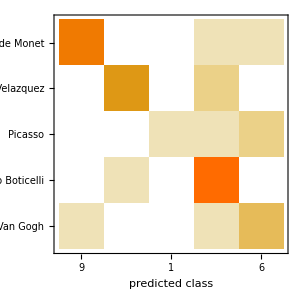

```mathematica
cmeasurements["Accuracy","Uncertainty"-> True]
cmeasurements["ConfusionMatrixPlot"]
```

It can be seen that the classifier confuses Vincent Van Gogh with Claude Monet, the most closely related styles from the five presented, even though Post-Impressionism was a reaction to it’s predecessor movement, specially regarding the use of light an color in natural environments. The classifier and machine learning algorithms does not know this, but it may associate some of the recursive themes in both movements.

If we used the classifier function with van Gogh’s “The Yellow House” we would probably see Monet Van Gogh and Claude Monet as the two most probable ones.

```mathematica
ReverseSort@cfunction[-Graphics-,"Probabilities"]
```

<|Vincent Van Gogh→0.793303,Sandro Boticelli→0.11186,Claude Monet→0.0544579,Picasso→0.0347152,Diego Velazquez→0.00566394|>

We could apply the classifier function to any painting or image that is not in the training set. For instance classifying a picture of myself would result in the a classification that associates to either Van Gogh, Diego Velazquez or Picasso. In my defense , given I may not look like the distorted and abstract figures Picasso painted, this classification could be due to the mix of color of the image, which would be more closely related to these painters artwork.

```mathematica
ReverseSort@cfunction[-Graphics-,"Probabilities"]
```

<|Picasso→0.849905,Vincent Van Gogh→0.0696176,Diego Velazquez→0.047474,Claude Monet→0.028678,Sandro Boticelli→0.00432565|>

## Feature Extraction and Space Plot

Built-in functions that relate more to unsupervised learning can be used to see how paintings are separated depending on features extracted by different algorithms. For instance one could extract different features from a training set represented as a vector or finite list of values.

```mathematica
fextraction=FeatureExtraction[Keys@trainingset]
```

FeatureExtractorFunction[…]

Now we can apply this function to an image from the same set and see how the function generates a set of values in a large vector or list.

```mathematica
Keys@trainingset[[2]]
fextraction[%]
```

-Graphics-

{-0.958208,0.353367,0.445149,-0.995976,-1.49061,0.121819,-0.854184,-1.11669,-0.2541,-0.536443,0.0177441,0.043412,-1.40154,1.35249,0.198912,-0.0959333,0.384165,1.37025,0.488027,0.639749,-0.814206,-0.722188,0.215327,0.540511,1.57705,-0.419666,-0.564311,0.577348,-0.191409,-0.133426,0.434158,0.507397,-1.8801,-0.561473,-0.399997,-0.20816,1.06804,-0.696449,-0.091155,0.551302,-0.104116,0.528565,-0.0198615,0.756271,0.247666,-1.24666,-0.880495,0.626499,-1.45085,1.03157,0.733728,1.21775,0.772326,1.81133,0.362102,-0.139373,1.01865,0.556102,0.156033,-1.32689,0.659365,-0.223681,1.6554,-1.65971,0.779723,-0.848794,-0.645378,-0.589023,1.06302,-1.4798,-0.898993,1.02787,0.267342,-2.54406,0.90468,0.555337,-1.50915,0.797135,1.54635,-0.477266,1.18217,-0.800683,-0.671371,0.00371685,-1.00089,1.42527,1.34957,-0.416867,-1.35734,0.759589,-0.891695,-2.40319,-1.40801,-1.263,-0.532163,-0.51807,0.710307,-0.8743,-0.795498,-0.322221,-1.50546,1.1556,1.09458,0.622172,-0.12153,-1.28418,-1.59664,1.57917,1.44111,-1.38504,-0.0822487,-2.41099,-0.110878,0.424624,0.383623,-1.384,-0.093734,-1.91742,-0.0223622,1.41992,0.0509186,1.61699,2.55146,-0.634789,0.668691,-1.96623,-0.818819,-0.00208227,-1.46752,0.143483,-0.636068,-0.912641,0.990253,0.229831,0.265449,0.0404083,-0.342912,0.665079,-0.0173127}

We can also visualize this parametrization of the features in the images by a space plot.

```mathematica
Iconize[{LabelingFunction->(Callout[ImageResize[#,200],Automatic]&)}]
```

```mathematica
FeatureSpacePlot[Keys@trainingset,ImageSize->Large,]
```

-Graphics-

As expected we can see groups of paintings from the same artist closer together. Alternatively, Impressionist paintings and landscapes can be seen to be on the opposite side and edge of those from portraits from the Baroque and Renaissance period.

To be able to see the different artist the feature Space Plot know will show points with a label of the first letter of the painter name.

```mathematica
letterToColor=Thread[StringTake[#,{1}]&/@paintersList->colors];
Iconize[{ImageSize->Large,
LabelingFunction->(With[{letter=StringTake[trainingset⟦#2⟦2⟧,2⟧,1]},Style[Text[letter],letter/.letterToColor]]&)
,PlotStyle->Opacity[0.5]}]
Iconize[g/.{GraphicsGroup[{___,x:Text[___]}]:>GraphicsGroup[{x}],Point[___]:>{},Offset[{_,_},x_]:>Offset[{0,0},x]}]
```

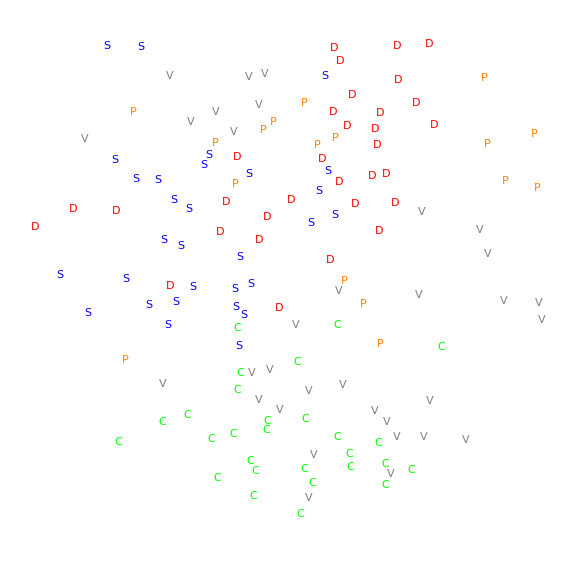

```mathematica
g=FeatureSpacePlot[Keys[trainingset],];
g2=
```

Similar to our first plot it can be seen how artists from the Baroque and the Renaissance are closer together in the plot, while Monet and Van Gogh are mixed together, again due to a similarity in style.

## Search

This code uses the feature extraction tools applied before to generate a function that, in this case, finds the image with the  nearest features. This could be though of as the shortest distance between two vectors in a multidimensional space.

```mathematica
searchdataset=Keys@trainingset;
nearestf=FeatureNearest[searchdataset]
```

NearestFunction[…]

Again we can apply it to a picture of myself and see the resemblance.

```mathematica
First@nearestf[-Graphics-]
```

-Graphics-

Following the link, you could also upload an image of yourself or even one of your paintings, in the following API deployed to the cloud. You can see what painting from 5 of the most famous painters in history has the nearest features.

```mathematica
CloudDeploy[TestF=FormFunction[{"l"->"Image"},First@nearestf[#l]&]
]
```

CloudObject[https://www.wolframcloud.com/objects/d6f58362-fd48-4130-8b06-0e2da8ef5378]

## Further explorations

Recent articles show studies of how machine learning algorithms differentiate between various styles of painting and movements in art history. It is quite interesting to understand how the algorithms differentiate and classify artworks. The tools in the Wolfram Language could be useful for this purpose.

https://arxiv.org/pdf/1801.07729.pdf

https://arxiv.org/abs/1706.07068

## Author contact information

Diego Gutierrez Coronel

06/28/2018

dgutie10@hawk.iit.edu

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)